Решение уравнения имеет вид: t+(8 t^2)/189

Найденная функция является решением уравнения

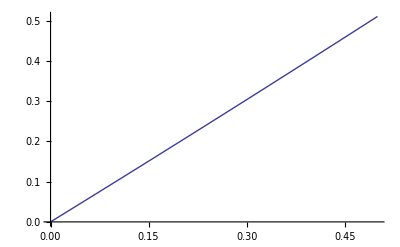

```mathematica
(*Зададим параметр λ*)
λ=1;
(*Зададим отрезок интегрирования*)
a=0;
b=1/2;
(*Зададим ядро уравнения*)
K[s_,t_]=t^2*s;
(*Зададим функции, входящие в вырожденное ядро уравнения*)
P={t^2};
Q={s};
(*Зададим свободный член уравнения*)
f[t_]=t;
(*Найдем количество слагаемых в ядре уравнения*)
n=Dimensions[P][[1]];
(*Построим матрицу Фредгольма*)B=Table[Integrate[Q[[k]]*ReplaceAll[P[[j]],t->s],{s,a,b}],{k,1,n},{j,1,n}];
IM=IdentityMatrix[n];
F=IM-λ*B;
(*Зададим столбец свободных членов*)
A=Table[Integrate[f[s]*Q[[k]],{s,a,b}],{k,1,n}];
(*Найдем коэффициенты решения уравнения*)
c=Inverse[F].A;
(*Построим решение данного уравнения*)
x[t_]=f[t]+λ*Sum[c[[j]]*P[[j]],{j,1,n}];
Print["Решение уравнения имеет вид: ",x[t]]
(*Выполним проверку*)
If[FullSimplify[x[t]-λ*Integrate[K[s,t]*x[s],{s,a,b}]-f[t]]==0,
Print["Найденная функция является решением уравнения"],
Print["Ищи ошибку"]]
(*Построим график решения уравнения*)
G=Plot[x[t],{t,a,b}]
```